(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1
-1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1
1 | -1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1
-1 | -1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | 1
-1 | -1 | 1 | 1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | 1 | 1 | -1)

6

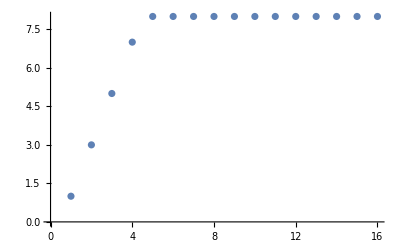

```mathematica
ClearAll[MakeQ]

MakeQ[N_,m_]:=Module[{allPatterns,psiSet,phiSet,xiList,Q},(*all 2^N binary vectors with entries {-1,1}*)allPatterns=Tuples[{-1,1},N];
(*randomly choose m of them for psi and phi*)
psiSet=RandomSample[allPatterns,m];
phiSet=RandomSample[allPatterns,m];
(*all m^2 concatenated vectors*)
xiList=Flatten[Table[Join[psiSet[[i]],phiSet[[j]]],{i,m},{j,m}],1];
(*columns are xi vectors*)Q=Transpose[xiList];
<|"Q"->Q,"Dimensions"->Dimensions[Q],"Rank"->MatrixRank[Q]|>]

Qout =MakeQ[3,5];
Qout[["Q"]]//MatrixForm
Qout[["Rank"]]

ListPlot[Table[{i,MakeQ[4,i][["Rank"]]},{i,1,16}]]
```